```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]],"Data"]];
Clear[AllFiles,FileData1,len1,f];AllFiles=Sort[FileNames["*.csv"]];len1=Length[AllFiles];
For[i=1,i≤len1,i++,{f=Import[AllFiles[[i]]];FileData1[i]=Take[f,{1,-1}],Clear[f]}];
```

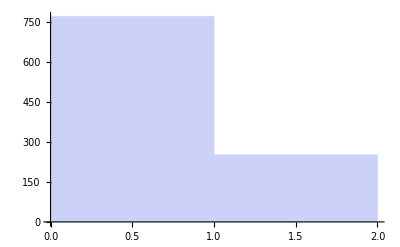
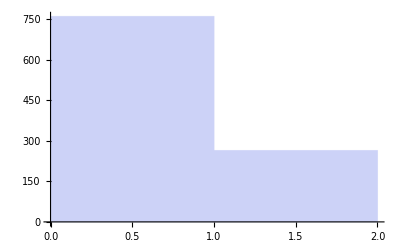
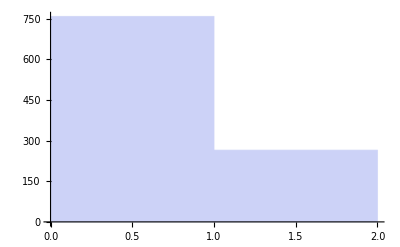
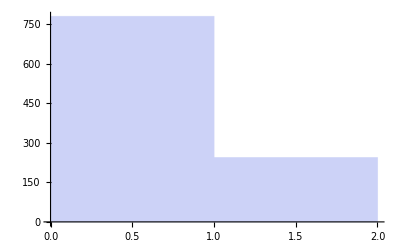

```mathematica
{Histogram[FileData1[1][[1]]],Histogram[FileData1[1][[2]]],Histogram[FileData1[1][[3]]]Histogram[FileData1[1][[4]]]}
```

```mathematica
Sum[FileData1[3][[1]][[k]],{k,1,1024}]
```

270

```mathematica
Vv={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
Y={{0,-ⅈ},{ⅈ,0}};Z={{1,0},{0,-1}};X={{0,1},{1,0}};
```

```mathematica
Clear[z,x,y];For[i=1,i≤len1,i++,{Clear[MM];MM=Table[Table[{Vv[[FileData1[i][[j]][[k]]+1]]},{k,1,Length[FileData1[i][[j]]]}],{j,1,4}];z[i][1]=Table[MM[[1]][[k]].Z.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
z[i][2]=Table[MM[[2]][[k]].Z.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
z[i][3]=Table[MM[[3]][[k]].Z.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
z[i][4]=Table[MM[[3]][[k]].Z.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];
y[i][1]=Table[MM[[1]][[k]].Y.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
y[i][2]=Table[MM[[2]][[k]].Y.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
y[i][3]=Table[MM[[3]][[k]].Y.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
y[i][4]=Table[MM[[3]][[k]].Y.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];
x[i][1]=Table[MM[[1]][[k]].X.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
x[i][2]=Table[MM[[2]][[k]].X.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
x[i][3]=Table[MM[[3]][[k]].X.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
x[i][4]=Table[MM[[3]][[k]].X.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];}]
```

```mathematica
Manipulate[{Clear[YY];YY=Table[Flatten[ConjugateTranspose[y[m][k]]].y[m][i],{i,1,4},{k,1,4}];XYZ1[i]=Flatten[YY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ1[i]],Tr[XYZ1[i]]},{m,1,len1,1}]
```

```mathematica
Manipulate[{Clear[ZZ];ZZ=Table[Flatten[ConjugateTranspose[z[m][k]]].z[m][i],{i,1,4},{k,1,4}];XYZ2[i]=Flatten[ZZ,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ2[i]],Tr[XYZ2[i]],Det[XYZ2[i]]},{m,1,len1,1}]
```

```mathematica
Manipulate[{Clear[XY];XY=Table[Flatten[ConjugateTranspose[x[m][k]]].y[m][i],{i,1,4},{k,1,4}];XYZ3[i]=Flatten[XY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ3[i]],Tr[XYZ3[i]],Det[XYZ3[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[ZX];ZX=Table[Flatten[ConjugateTranspose[z[m][k]]].x[m][i],{i,1,4},{k,1,4}];XYZ4[i]=Flatten[ZX,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ4[i]],Tr[XYZ4[i]],Det[XYZ4[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[ZY];ZY=Table[Flatten[ConjugateTranspose[z[m][k]]].y[m][i],{i,1,4},{k,1,4}];XYZ5[i]=Flatten[ZY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ5[i]],Tr[XYZ5[i]],Det[XYZ5[i]]},{m,1,3,1}]
```

```mathematica
Det[XYZ[2]]
```

71090738947825408

```mathematica
Inv[a_]:=If[a==0,1,0]
```